```mathematica
Solve[((1-x^2) Cos[σ])/(2 *x-2 Cos[σ] *x^2)==1,x]
```

{{x→-1/2 Sec[σ] (-2-2 Sin[σ])},{x→-1/2 Sec[σ] (-2+2 Sin[σ])}}

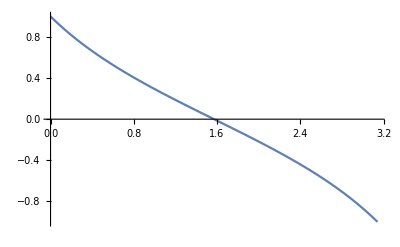

```mathematica
Plot[{ Sec[σ] (1- Sin[σ])},{σ,0,π}]
```

```mathematica
ProductHermitian[v1_, v2_, α_, ω_,τ_]:= Conjugate[v1].{{Cos[α-ω*τ]^2+Sin[ω*τ]^2,-2 ⅈ Sin[α] Sin[ω*τ]^2},{2 ⅈ Sin[α] Sin[ω*τ]^2,Cos[α+ω*τ]^2+Sin[ω*τ]^2}}.Transpose[v2] Sec[α]^2
Evolution= {{Cos[ω*τ-α],-ⅈ*Sin[ω*τ]},{-ⅈ*Sin[ω*τ],Cos[α+ω*τ]}}*Sec[α]
EvolutionConjugated= Transpose[{{Cos[ω*τ-α],ⅈ*Sin[ω*τ]},{ⅈ*Sin[ω*τ],Cos[α+ω*τ]}}*Sec[α]]
v1Ref ={{Cos[1/4 (π-2 σ)],-ⅈ Sin[1/4 (π-2 σ)]}}
v2Ref ={{Cos[1/4 (π+2 σ)],-ⅈ Sin[1/4 (π+2 σ)]}}
v1Probe={{Cos[1/4 (π+2 δ)],-ⅈ Sin[1/4 (π+2 δ)]}}
```

{{Cos[α-τ ω] Sec[α],-ⅈ Sec[α] Sin[τ ω]},{-ⅈ Sec[α] Sin[τ ω],Cos[α+τ ω] Sec[α]}}

{{Cos[α-τ ω] Sec[α],ⅈ Sec[α] Sin[τ ω]},{ⅈ Sec[α] Sin[τ ω],Cos[α+τ ω] Sec[α]}}

{{Cos[1/4 (π-2 σ)],-ⅈ Sin[1/4 (π-2 σ)]}}

{{Cos[1/4 (π+2 σ)],-ⅈ Sin[1/4 (π+2 σ)]}}

{{Cos[1/4 (π+2 δ)],-ⅈ Sin[1/4 (π+2 δ)]}}

```mathematica
τ=π/(2*ω)
```

π/(2 ω)

```mathematica
α=ArcSin[(1-Sin[σ])/Cos[σ]]
```

ArcSin[Sec[σ] (1-Sin[σ])]

```mathematica
τ =ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]/ω
```

ArcSin[√((Cos[σ] (1-Sec[σ]^2 (1-Sin[σ])^2))/(2 Sec[σ] (1-Sin[σ])-2 Sec[σ] (1-Sin[σ])^2))]/ω

```mathematica
FullSimplify[ArcSin[√((Cos[σ] (1-Sec[σ]^2 (1-Sin[σ])^2))/(2 Sec[σ] (1-Sin[σ])-2 Sec[σ] (1-Sin[σ])^2))]]
```

π/2

```mathematica
cosFirst=FullSimplify[(Abs[ProductHermitian[v1Ref,v1Probe,α, ω, τ]])^2/(ProductHermitian[v1Ref,v1Ref,α, ω, τ]*ProductHermitian[v1Probe,v1Probe,α, ω, τ]), {σ∈Reals,δ∈Reals}]
```

{{(-1+Cos[δ-σ])/(-2+2 Cos[δ] Cos[σ])}}

```mathematica
cosFirstFunction[δ_,σ_]:= (1-Cos[δ-σ])/(2-2 Cos[δ] Cos[σ])
```

```mathematica
EvolutionMT=FullSimplify[{{Cos[α+ω*τ] Sec[α],ⅈ Sec[α] Sin[ω*τ]},{ⅈ Sec[α] Sin[ω*τ],Cos[α-ω*τ] Sec[α]}}, {σ∈Reals,δ∈Reals, σ>0}]
```

{{-Cot[σ] √(1/(2+2 Csc[σ])),ⅈ/(2 √(1/(2+2 Csc[σ])))},{ⅈ/(2 √(1/(2+2 Csc[σ]))),Cot[σ] √(1/(2+2 Csc[σ]))}}

```mathematica
LeftEvolutionMT=FullSimplify[{{Cos[α+ω*τ] Sec[α],-ⅈ *Sec[α] Sin[ω*τ]},{-ⅈ *Sec[α] Sin[ω*τ],Sec[α] Cos[α-ω*τ]}}, {σ∈Reals,δ∈Reals, σ>0}]
```

{{-Cot[σ] √(1/(2+2 Csc[σ])),-ⅈ/(2 √(1/(2+2 Csc[σ])))},{-ⅈ/(2 √(1/(2+2 Csc[σ]))),Cot[σ] √(1/(2+2 Csc[σ]))}}

```mathematica
MatrixForm[FullSimplify[LeftEvolutionMT.EvolutionMT]]
```

(Csc[σ] | -ⅈ Cot[σ]
ⅈ Cot[σ] | Csc[σ])

```mathematica
Unit={{1,0},{0,1}}
```

{{1,0},{0,1}}

```mathematica
Nm=(N0*FullSimplify[LeftEvolutionMT.EvolutionMT])
ZetaF=MatrixPower[Nm-Unit,1/2]
```

{{N0 Csc[σ],-ⅈ N0 Cot[σ]},{ⅈ N0 Cot[σ],N0 Csc[σ]}}

{{(Cot[σ/2] √(-1+N0 Cot[σ/2]) Cot[σ] (-Sec[σ]+Cot[σ/2] Tan[σ]))/(-1+Cot[σ/2]^2)-(Cot[σ/2] Cot[σ] √(-1+N0 Tan[σ/2]) (-Sec[σ]+Tan[σ/2] Tan[σ]))/(-1+Cot[σ/2]^2),(ⅈ √(-1+N0 Cot[σ/2]) (Csc[σ]-Tan[σ/2]) Tan[σ/2] (-Sec[σ]+Cot[σ/2] Tan[σ]))/(-1+Tan[σ/2]^2)-(ⅈ Cot[σ/2] (Cot[σ/2]-Csc[σ]) √(-1+N0 Tan[σ/2]) (-Sec[σ]+Tan[σ/2] Tan[σ]))/(-1+Cot[σ/2]^2)},{(ⅈ Cot[σ/2] √(-1+N0 Cot[σ/2]) Cot[σ])/(-1+Cot[σ/2]^2)-(ⅈ Cot[σ/2] Cot[σ] √(-1+N0 Tan[σ/2]))/(-1+Cot[σ/2]^2),(Cot[σ/2] (Cot[σ/2]-Csc[σ]) √(-1+N0 Tan[σ/2]))/(-1+Cot[σ/2]^2)-(√(-1+N0 Cot[σ/2]) (Csc[σ]-Tan[σ/2]) Tan[σ/2])/(-1+Tan[σ/2]^2)}}

```mathematica
N0=Cot[σ/2]
```

Cot[σ/2]

```mathematica
FullSimplify[ZetaF,0<σ<π/2]
```

{{1/2 √Cos[σ] Csc[σ/2],-1/2 ⅈ √Cos[σ] Csc[σ/2]},{1/2 ⅈ √Cos[σ] Csc[σ/2],1/2 √Cos[σ] Csc[σ/2]}}

```mathematica
EvolvedFirst=FullSimplify[Evolution.Transpose[v1Probe]]
```

{{(-Sin[1/4 (π+2 δ)]+Cos[1/4 (π+2 δ)] (Sec[σ]-Tan[σ]))/(√2 √(1/(1+Csc[σ])))},{-(ⅈ (Cos[1/4 (π+2 δ)]+Sin[1/4 (π+2 δ)] (-Sec[σ]+Tan[σ])))/(√2 √(1/(1+Csc[σ])))}}

```mathematica
ZetaEvolvedFirst=FullSimplify[ZetaF.Evolution.Transpose[v1Probe]]
```

{{-(Cos[δ/2] (-1+Cot[σ/2]))/(√(Cos[σ] Csc[σ/2]^2) √(1/(1+Csc[σ])))},{-(ⅈ Cos[δ/2] (-1+Cot[σ/2]))/(√(Cos[σ] Csc[σ/2]^2) √(1/(1+Csc[σ])))}}

```mathematica
EvolvedFirstNormSq=FullSimplify[Abs[EvolvedFirst[[1]][[1]]]^2+Abs[EvolvedFirst[[2]][[1]]]^2, {σ∈Reals,δ∈Reals, σ>0}]
```

1/2 Abs[1+Csc[σ]] (Abs[Sin[1/4 (π+2 δ)]+Cos[1/4 (π+2 δ)] (-Sec[σ]+Tan[σ])]^2+Abs[Cos[1/4 (π+2 δ)]+Sin[1/4 (π+2 δ)] (-Sec[σ]+Tan[σ])]^2)

```mathematica
EvolvedFirstNormSq = FullSimplify[1/2 *(1+Csc[σ])*((Sin[1/4 (π+2 δ)]+Cos[1/4 (π+2 δ)] (-Sec[σ]+Tan[σ]))^2+(Cos[1/4 (π+2 δ)]+Sin[1/4 (π+2 δ)] (-Sec[σ]+Tan[σ]))^2)]
```

-Cos[δ] Cot[σ]+Csc[σ]

```mathematica
ZetaEvolvedFirstNormSq=FullSimplify[Abs[ZetaEvolvedFirst[[1]][[1]]]^2+Abs[ZetaEvolvedFirst[[2]][[1]]]^2, {σ∈Reals,δ∈Reals, σ>0}]
```

(2 Abs[Cos[δ/2]^2 (-1+Cot[σ/2])^2 (1+Csc[σ])])/Abs[Cos[σ] Csc[σ/2]^2]

```mathematica
ZetaEvolvedFirstNormSq=(2 *Cos[δ/2]^2 (-1+Cot[σ/2])^2 (1+Csc[σ]))/(Cos[σ] Csc[σ/2]^2)
```

2 Cos[δ/2]^2 (-1+Cot[σ/2])^2 (1+Csc[σ]) Sec[σ] Sin[σ/2]^2

```mathematica
ZetaEvolvedFirstNormSq=FullSimplify[(2 *Cos[δ/2]^2 (-1+Cot[σ/2])^2 (1+Csc[σ]))/(Cos[σ] Csc[σ/2]^2)]
```

2 Cos[δ/2]^2 (-1+Csc[σ]) (1+Csc[σ]) Tan[σ]

```mathematica
DecisivenessFirst=FullSimplify[EvolvedFirstNormSq/(EvolvedFirstNormSq+ZetaEvolvedFirstNormSq),{0<σ<π/2,0<δ<π/2}]
```

2 Csc[σ] (-Cos[δ] Cot[σ]+Csc[σ]) Sin[σ/2]^2

```mathematica
FullSimplify[DecisivenessFirst-(1/2)*(1- Cos[δ]*Cos[σ])Sec[σ/2]^2]
```

0

```mathematica
DecisivenessFunction[δ_,σ_]:=2 Csc[σ] (-Cos[δ] Cot[σ]+Csc[σ]) Sin[σ/2]^2
```

```mathematica
FullSimplify[DecisivenessFunction[σ,σ]]
```

1-Cos[σ]

```mathematica
FullSimplify[DecisivenessFunction[-σ,σ]]
```

1-Cos[σ]

```mathematica
N0=Tan[σ/2]
```

Tan[σ/2]

```mathematica
FullSimplify[ZetaF,π/2<σ<π]
```

{{1/(√2 √(-1-Sec[σ])),ⅈ/(√2 √(-1-Sec[σ]))},{-ⅈ/(√2 √(-1-Sec[σ])),1/(√2 √(-1-Sec[σ]))}}

```mathematica
Eigenvalues[{{1/(√2 √(-1-Sec[σ])),ⅈ/(√2 √(-1-Sec[σ]))},{-ⅈ/(√2 √(-1-Sec[σ])),1/(√2 √(-1-Sec[σ]))}}]
```

```mathematica
EvolvedFirst=FullSimplify[Evolution.Transpose[v1Probe],π/2<σ<π]
```

{{-(√(1+Csc[σ]) (Sin[1/4 (π+2 δ)]+Cos[1/4 (π+2 δ)] (-Sec[σ]+Tan[σ])))/(√2)},{-(ⅈ √(1+Csc[σ]) (Cos[1/4 (π+2 δ)]+Sin[1/4 (π+2 δ)] (-Sec[σ]+Tan[σ])))/(√2)}}

```mathematica
ZetaEvolvedFirst=FullSimplify[ZetaF.Evolution.Transpose[v1Probe],π/2<σ<π]
```

{{-(√2 Cos[σ/2] √(-(Cos[σ]+Cot[σ])/(1+Cos[σ])) Sin[δ/2])/(Cos[σ/2]+Sin[σ/2])},{ⅈ √2 Cos[σ/2] (-1+Cot[σ/2]) √(-(Cos[σ]+Cot[σ])/(1+Cos[σ])) Sec[σ] Sin[δ/2] Sin[σ/2]}}

```mathematica
EvolvedFirstNormSq=FullSimplify[Abs[EvolvedFirst[[1]][[1]]]^2+Abs[EvolvedFirst[[2]][[1]]]^2, {π/2<σ<π,δ∈Reals}]
```

-Cos[δ] Cot[σ]+Csc[σ]

```mathematica
ZetaEvolvedFirstNormSq=FullSimplify[Abs[ZetaEvolvedFirst[[1]][[1]]]^2+Abs[ZetaEvolvedFirst[[2]][[1]]]^2, {π/2<σ<π,δ∈Reals}]
```

(-1+Cos[δ]) Cot[σ]

```mathematica
DecisivenessFirst=FullSimplify[EvolvedFirstNormSq/(EvolvedFirstNormSq+ZetaEvolvedFirstNormSq),{π/2<σ<π}]
```

(Cos[δ] Cot[σ]-Csc[σ])/(Cot[σ]-Csc[σ])

```mathematica
FullSimplify[DecisivenessFirst-(1/2)*(1- Cos[δ]*Cos[σ])Csc[σ/2]^2]
```

0